# Tornadi v ZDA

## Pridobivanje podatkov

Podatke sem pridobil iz Wolfram Data Repository.

```mathematica
podatki=ResourceData["Tornadoes in the U.S., 1950-2015"]
```

Dataset[<>]

## Analiza glede na drzave

```mathematica
podatki[1]
```

Drzave z najvecjim stevilom tornadov .

```mathematica
drzave=ReverseSortBy[Tally[#["Location"]&/@podatki],Last]
```

Iz zgornje tabele in spodnje slike lahko opazimo, da se tornadi v ZDA najpogosteje pojavljajo v Texasu.

```mathematica
GeoRegionValuePlot[drzave,PlotLabel->"Stevilo tornadov po drzavah",ImageSize->{900,450},ColorFunction->"TemperatureMap"]
```

-Graphics-

Drzava z najmajnsim stevilom tornadov (1950 - 2015)

```mathematica
Select[drzave,#[[2]]==Min[drzave[All,2]]&]
```

## Analiziranje stevila ranjenih oz . mrtvih

```mathematica
ranjeni=podatki[All,"Injuries"]
```

Dataset[<>]

```mathematica
umrli = podatki[All, "Fatalities"]
```

Dataset[<>]

Celotni število ranjenih.

```mathematica
Total[ranjeni]
```

107099

Celotno število umrlih .

```mathematica
Total[umrli]
```

6851 people

Iz zgornjih dveh števil lahko vidimo, da je število umrlih pri pojavitvah tornadov veliko manjše kot število ranjenih kar je dobro.

Število ranjenih in umrlih za določeno državo (npr. Texas)

```mathematica
Prikaz[lokacija_]:=Total[podatki[Select[#"Location"==lokacija &],{6,7}]]
```

```mathematica
Prikaz[Entity["AdministrativeDivision",{"Texas","UnitedStates"}]]
```

<|Injuries→11075,Fatalities→634 people|>

## Magnitude tornadov

Število tornadov z določeno magnitudo.

```mathematica
vse = podatki[All, "Magnitude"];
```

```mathematica
Mag[magnituda_]:= {magnituda, Count[vse, magnituda]}
```

```mathematica
stvseh= SortBy[Mag/@(vse//DeleteDuplicates), Last]
```

Lestvica F temelji na količini škode, ki jo povzroči tornado, medtem ko se lestvica EF  se bolj zanaša na hitrost vetra za določanje tornada.

Vidimo lahko, da je bilo največ tornadov tipa F0 in F1 kateri povzročijo lahko oz. zmerno škodo.

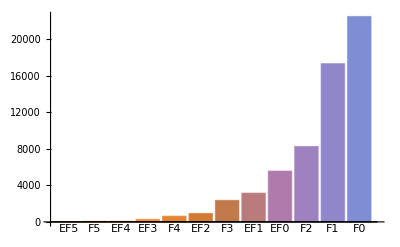

```mathematica
BarChart[{{11,77,81,284,628,924,2363,3155,5570,8265,17343,22516}},ChartLabels->{"EF5","F5","EF4","EF3","F4","EF2","F3","EF1", "EF0", "F2","F1","F0"}]
```

## Število ranjenih skozi leta v Texasu

```mathematica
teksas= podatki[Select[#"Location"==Entity["AdministrativeDivision",{"Texas","UnitedStates"}]&],{3, 6}]
```

Dataset[<>]

```mathematica
Max[teksas[All,{2}]]
```

1740

Največje število ranjenih je zaradi tornadi je bilo kar 1740 in 42 mrtvih.

```mathematica
Select[podatki,#["Injuries"]==1740&]
```

Vidimo, da je bil tornado kar z magnitudo F4 in da so bile skode ogromne, hitrosti taksnih tornadov presegajo 350km/h.

## Materialne Škode (od leta 2010 do 2015) v Texasu

```mathematica
podatki2 = podatki[54145;;]
```

Dataset[<>]

```mathematica
fun[drzava_]:=podatki2[Select[#"Location"==drzava&],{1,8}]
```

```mathematica
tab2 = fun[Entity["AdministrativeDivision",{"Texas","UnitedStates"}]]
```

Skupna vredno škode.

```mathematica
Total[tab2[All,{2}]]
```

<|EstimatedPropertyLoss→407 Missing[NotAvailable]+1.14069×10^9 $|>

```mathematica
Max[tab2[All,{2}]]
```

Max[Missing[NotAvailable],4.00003×10^8 $]

Vidimo lahko, da so škode zaradi tornadov lahko zelo velike.

## Število tornadov skozi leta

Katerega leta je bilo največ tornadov.

```mathematica
datumi=podatki[All,"Date"];
```

```mathematica
letnice=DateObject[#,"Year"]&/@datumi;
```

```mathematica
tabela=ReverseSortBy[Tally[#&/@letnice],Last]
```

Največje število tornadov je bilo leta 2004.

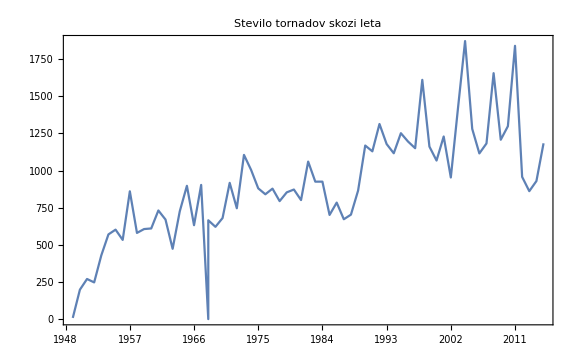

```mathematica
Show[DateListPlot[tabela, ImageSize -> Large, PlotLabel->"Stevilo tornadov skozi leta"]]
```

Skozi čas lahko opazimo, da se število tornadov nekoliko povečuje , kar ni dobro za prihodnost.

## Aplikacija v oblaku

Aplikacija bo za dano drzavo izrisala graf kateri bo prikazoval stevila tornadov od leta 1950 do 2015.

```mathematica
Graf[drzava_]:=Graphics[DateListPlot[ReverseSortBy[Tally[#&/@DateObject[#,"Year"]&/@Select[podatki,#["Location"]==drzava&][All,"Date"]],Last], ImageSize -> Large,PlotLabel->"Števila tornadov skozi leta v dani državi."]]
```

```mathematica
obrazec=FormPage["drzava"->"AdministrativeDivision",Graf[#drzava]&,AppearanceRules-><|"Title"->"Graf v odvisnosti od drzave",
				"Description"->"Vnesi ime ZDA države","SubmitLabel"->"Potrdi"|>];
```

```mathematica
CloudDeploy[obrazec,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/79083a85-b46b-40e2-afbc-416e4c78a379]